# Resonator Quantization Derivation

## Paths and packages;import files

Mathematica package

```mathematica
Needs["NumericalCalculus`"]
```

## Resonator Hamiltonian derivation

Variable definition

```mathematica
Im[Z0]^:=0;
Conjugate[Z0]^:=Z0;
Im[L]^:=0;
Conjugate[L]^:=L;
Im[ω]^:=0;
Conjugate[ω]^:=ω;
Im[Ctilde]^:=0;
Conjugate[Ctilde]^:=Ctilde;
Im[c]^:=0;
Conjugate[c]^:=c;
Im[l]^:=0;
Conjugate[l]^:=l;
Im[hbar]^:=0;
Conjugate[hbar]^:=hbar;
```

```mathematica
Ctilde=1/(Z0*c);
Γ=(I*ω*L-Z0)/(I*ω*L+Z0)
ΓDagger=Conjugate[Γ]
(*Exp[2*I ω/c l]=Γ*)
```

(-Z0+ⅈ L ω)/(Z0+ⅈ L ω)

(-Z0-ⅈ L ω)/(Z0-ⅈ L ω)

Transmission Line energy

```mathematica
eE=1/2*Ctilde*Integrate[(1/2*(vPlus*(Exp[-I*ω/c*z]+Γ*Exp[I*ω/c*z])+vPlusDagger*(Exp[I*ω/c*z]+ΓDagger*Exp[-I*ω/c*z])))^2,{z,-l,0}]
```

1/(8 c Z0 ω (Z0^2+L^2 ω^2)^2)(ⅈ (vPlus-vPlusDagger) Z0+L (vPlus+vPlusDagger) ω)^2 (2 ω (c L Z0+l (Z0^2+L^2 ω^2)-c L Z0 Cos[(2 l ω)/c])+c (-Z0+L ω) (Z0+L ω) Sin[(2 l ω)/c])

```mathematica
eE=1/(2 c Z0)(1/2 l (vPlusDagger+vPlus Γ) (vPlus+vPlusDagger ΓDagger)-(ⅈ c ΓDagger (-1+Γ) ((vPlusDagger+vPlus Γ)^2+Γ (vPlus+vPlusDagger ΓDagger)^2))/(8 ω));

Simplify[eE]
```

-((vPlus (Z0-ⅈ L ω)-vPlusDagger (Z0+ⅈ L ω))^2 (c L Z0+l (Z0^2+L^2 ω^2)))/(4 c Z0 (Z0^2+L^2 ω^2)^2)

```mathematica
eM=1/2*Ctilde*Integrate[(1/2*(vPlus*(Exp[-I*ω/c*z]-Γ*Exp[I*ω/c*z])+vPlusDagger*(Exp[I*ω/c*z]-ΓDagger*Exp[-I*ω/c*z])))^2,{z,-l,0}]
```

((vPlus (Z0-ⅈ L ω)+vPlusDagger (Z0+ⅈ L ω))^2 (-2 c L Z0+2 l (Z0^2+L^2 ω^2)+2 c L Z0 Cos[(2 l ω)/c]+(c (Z0-L ω) (Z0+L ω) Sin[(2 l ω)/c])/ω))/(8 c Z0 (Z0^2+L^2 ω^2)^2)

```mathematica
eM=1/(2 c Z0)(-1/2 l (vPlusDagger-vPlus Γ) (-vPlus+vPlusDagger ΓDagger)-(ⅈ c ΓDagger (-1+Γ) ((vPlusDagger-vPlus Γ)^2+Γ (vPlus-vPlusDagger ΓDagger)^2))/(8 ω));
Simplify[eM]
```

((vPlus (Z0-ⅈ L ω)+vPlusDagger (Z0+ⅈ L ω))^2 (-c L Z0+l (Z0^2+L^2 ω^2)))/(4 c Z0 (Z0^2+L^2 ω^2)^2)

```mathematica
eTL =eM+eE;
Simplify[eTL]
```

(l vPlus vPlusDagger)/(c Z0)+(L (-vPlus^2 (Z0-ⅈ L ω)^2-vPlusDagger^2 (Z0+ⅈ L ω)^2))/(2 (Z0^2+L^2 ω^2)^2)

Inductor energy

```mathematica
eL=L/8/Z0^2*((vPlus-vPlus*Γ)+(vPlusDagger-vPlusDagger*ΓDagger))^2;
Simplify[eL]
```

-(L (ⅈ vPlus Z0+ⅈ vPlusDagger Z0+L vPlus ω-L vPlusDagger ω)^2)/(2 (Z0^2+L^2 ω^2)^2)

Total energy

```mathematica
eTotal=Simplify[eTL+eL];
eTotalM=1/2 D[eTotal,{{vPlus,vPlusDagger},2}]
```

{{0,1/2 (l/(c Z0)+L/(Z0^2+L^2 ω^2))},{1/2 (l/(c Z0)+L/(Z0^2+L^2 ω^2)),0}}

Variable transformation

```mathematica
Clear[ΚDagger]
Clear[Κ]
q=Κ*vPlus+ΚDagger*vPlusDagger;
p=I*ω*Κ*vPlus+-I*ω*ΚDagger*vPlusDagger;
T={{Κ,ΚDagger},{I*ω*Κ,-I*ω*ΚDagger}};
transformedM=Simplify[Transpose[Inverse[T]].eTotalM.Inverse[T]]
```

{{(l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger),0},{0,(l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger ω^2)}}

```mathematica
MatrixForm[transformedM]
```

((l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger) | 0
0 | (l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger ω^2))

```mathematica
TeXForm[{{(l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger),0},{0,(l/(c Z0)+L/(Z0^2+L^2 ω^2))/(4 Κ ΚDagger ω^2)}}]
```

\left(
\begin{array}{cc}
 \frac{\frac{l}{c \text{Z0}}+\frac{L}{\text{Z0}^2+L^2 \omega ^2}}{4 K \text{KDagger}} & 0 \\
 0 & \frac{\frac{l}{c \text{Z0}}+\frac{L}{\text{Z0}^2+L^2 \omega ^2}}{4 K \text{KDagger} \omega ^2} \\
\end{array}
\right)

solve for transformation coefficients

```mathematica
ΚDagger=ΚDagger/.Solve[transformedM[[2,2]]==1/2 ,ΚDagger][[1,1]];
ΚDagger*Κ
```

(Κ (c L Z0+l Z0^2+l L^2 ω^2))/(2 (c Z0^3 Κ ω^2+c L^2 Z0 Κ ω^4))

in terms of creation and annihilation operators

```mathematica
Clear[vPlus]
Clear[vPlusDagger]
solution=Solve[p==I*Sqrt[hbar*ω]/Sqrt[2](aDagger-a)&&q==Sqrt[hbar]/Sqrt[2ω](aDagger+a),{vPlus,vPlusDagger}][[1]];
vPlus=vPlus/.solution;
vPlusDagger=vPlusDagger/.solution;
```

expression for current at the inductor end

```mathematica
current=(vPlus+vPlusDagger-Γ*vPlus-ΓDagger*vPlusDagger)/2/Z0;
Simplify[current]
```

(ⅈ aDagger l (Z0^2+L^2 ω^2) (-√hbar √ω+√(hbar ω))-ⅈ a l (Z0^2+L^2 ω^2) (√hbar √ω+√(hbar ω))+a c Z0 (-ⅈ √(hbar ω) (L-2 Z0^2 Κ^2 ω^2-4 ⅈ L Z0 Κ^2 ω^3+2 L^2 Κ^2 ω^4)+√hbar √ω (-2 ⅈ Z0^2 Κ^2 ω^2+2 ⅈ L^2 Κ^2 ω^4+L (-ⅈ+4 Z0 Κ^2 ω^3)))+aDagger c Z0 (ⅈ √(hbar ω) (L-2 Z0^2 Κ^2 ω^2-4 ⅈ L Z0 Κ^2 ω^3+2 L^2 Κ^2 ω^4)+√hbar √ω (-2 ⅈ Z0^2 Κ^2 ω^2+2 ⅈ L^2 Κ^2 ω^4+L (-ⅈ+4 Z0 Κ^2 ω^3))))/(2 √2 Κ ω (-ⅈ Z0+L ω) (c L Z0+l (Z0^2+L^2 ω^2)))

it happens that only ΚDagger = Κ/Γ makes the current operator only in terms of i (aDagger - a)

```mathematica
Κ=Sqrt[Γ(c L Z0+l Z0^2+l L^2 ω^2)/(2 (c Z0^3 ω^2+c L^2 Z0 ω^4))];
Simplify[current]
```

-(ⅈ (a-aDagger) hbar)/(√(hbar ω) (-ⅈ Z0+L ω) √((c L Z0+l (Z0^2+L^2 ω^2))/(c Z0 ω^2 (-ⅈ Z0+L ω)^2)))

```mathematica
TeXForm[-(ⅈ (a-aDagger)√(hbar ω c Z0))/(√(c L Z0+l (Z0^2+L^2 ω^2)))]
```

-\frac{i (a-\text{aDagger}) \sqrt{c \text{hbar} \omega  \text{Z0}}}{\sqrt{c L \text{Z0}+l \left(L^2 \omega
   ^2+\text{Z0}^2\right)}}

## Numerical Calculations

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["TunableResonator`"]
phi00 = 3.2897327*^-16;
c=1.149*^8;
Z0=52.3;
l=3364*^-6;
Ic=1187*^-9;
L =238.7*^-12;
beta=Ic*L/phi00;
mutual=61.1*^-12;
```

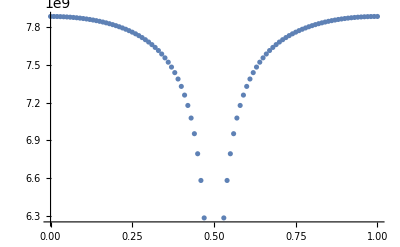

```mathematica
fs=Range[0, 1,0.01];
freqs=Table[resonatorFrequency[c,Z0,l,beta,Ic,f],{f,fs}];
ListPlot[Transpose[{fs,freqs}]]
```

```mathematica
TResVacuumFluctuations[c,Z0,l,beta,Ic,0]*mutual/phi00/2/Pi
```

{0.,0.000884942,0.}